```mathematica
SetDirectory[NotebookDirectory[]];
silver=<|"Date"->#1,"Value"->#2|>&@@@Import["quote-download/XAG.csv", "Table"]//Rest;
decisionsRawWithSchema=Import["ag-lm-1.csv", "Data"];
(*With[{dates=First/@silver, n=Length@silver}, Transpose[{dates,  RandomReal[{-5,5}, n],RandomReal[{0.25,10}, n]}]];
First/@silver ==First/@decisions*)
sparseRawWithSchema=Import["lasso-ag-1.csv", "Data"];
```

```mathematica
trainRaw=Import["train.csv","Data"];
```

```mathematica
trainRaw[[1]]
```

{dates.22.584.,X1,pred...1.,pred...2.,actual}

```mathematica
decisionsRawWithSchema[[1]]
```

{,as.Date(dates[783:804]),ex/100,upper/100,lower/100,actuals/100}

```mathematica
sparseRawWithSchema[[1]]
```

{,dates.585.805.,as.vector.pred1...1..,as.vector.pred1...2..,as.vector.pred1...3..,as.vector.act1.}

```mathematica
decisionsRaw=Rest@decisionsRawWithSchema;
logNormalVar[mu_,var_]:=(Exp[var]-1)Exp[2mu+var];
decisions=With[{dates=decisionsRaw[[All,2]],meanLogReturns=decisionsRaw[[All,3]],varLogReturns=((decisionsRaw[[All,4]]-decisionsRaw[[All,5]])/(2*2 (*95% ci*)))^2},<|"Date"->#1,"Return"->#2,"Var"->#3|>&@@@Transpose@{dates,Exp[meanLogReturns]-1,MapThread[logNormalVar,{meanLogReturns,varLogReturns}]}];
```

```mathematica
sparseRaw=Rest@sparseRawWithSchema;
sparse=<|"Date"->#2,"Returns"->Exp[#3]-1|>&@@@sparseRaw;
```

```mathematica
train=<|"Date"->#1,"Returns"->Exp[#3]-1|>&@@@Rest@trainRaw;
```

```mathematica
joined=JoinAcross[decisions, silver,Key["Date"],"Left"];
joinedSparse=JoinAcross[sparse, silver,Key["Date"],"Left"];
```

```mathematica
Length@joined
Length@joinedSparse
```

22

221

```mathematica
pp[x_]:=Prepend[x,First@x]
```

```mathematica
invest=1000000;
makeInvestment[{money_,ownedCommodities_}, {leverage_, currPrice_}]:=With[{toSell=ownedCommodities*currPrice},With[{newMoney=money+toSell},
With[{toSpend=newMoney*leverage},
With[{newCommodities=toSpend/currPrice},
{newMoney-toSpend, newCommodities}]]]]
state=FoldList[makeInvestment, {invest,0}, {#["Return"]/stddev^2,#["Value"]}&/@joined];
prices=pp[#["Value"]&/@joined];
value=First/@state+Last/@state*prices;
Last@value -10^6
```

0.+6.37306/stddev^2+(0.0000158805 (1.×10^6+6.37306/stddev^2))/stddev^2+26+(0.0000620845 (1.×10^6+6.37306/stddev^2+27))/stddev^2-(0.000242275 (1.×10^6+6.37306/stddev^2+(0.0000158805 (1))/stddev^2+26+(0.0000620845 (1.×10^6+28))/stddev^2))/stddev^2
 |  |  |  |

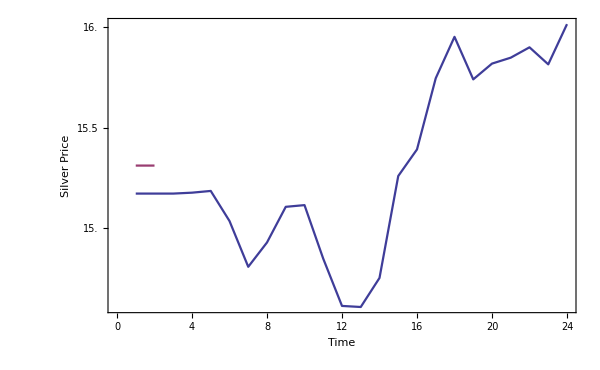
-Graphics-Ag PriceNet ValueTime

```mathematica
Labeled[Labeled[Labeled[TwoAxisListPlot[{pp@prices,value},{{Joined->True,ImageSize->600,AxesLabel->{"Time","Silver Price"}}, {Joined->True,ImageSize->600,AxesLabel->{"Time", "Net Value"}}}],"Ag Price", Left],"Net Value", Right],"Time", Bottom]
```

```mathematica
silver[[3]]
```

<|Date→2013-01-03,Value→30.9269|>

```mathematica
sparse[[1]]
```

<|Date→2015-02-03,Returns→-0.000640045|>

```mathematica
sparse//Last
```

<|Date→2015-10-15,Returns→0.000213739|>

```mathematica
train[[3]]
```

<|Date→4/29/2013,Returns→-0.0885971|>

```mathematica
stddev=#["Value"]&/@silver//StandardDeviation
```

4.14017

```mathematica
stddev=#["Returns"]&/@train//StandardDeviation
```

0.0610872

```mathematica
invest=15;
makeInvestmentSparse[{money_,ownedCommodities_},{edge_,currPrice_}]:=
With[{toSell=ownedCommodities*currPrice},With[{newMoney=money+toSell},
With[{toSpend=newMoney * edge/stddev^2},
With[{newCommodities=toSpend/currPrice},
{newMoney-toSpend, newCommodities}]]]]
stateSparse=FoldList[makeInvestmentSparse,{invest, 0},{#["Returns"],#["Value"]}&/@joinedSparse];
pricesSparse=pp[#["Value"]&/@joinedSparse];
valueSparse=First/@stateSparse+stateSparse[[All,2]]*pricesSparse;
```

```mathematica
(valueSparse-invest)/invest//Last
```

0.00726764

```mathematica
(valueSparse-invest)/invest//StandardDeviation
```

0.00740725

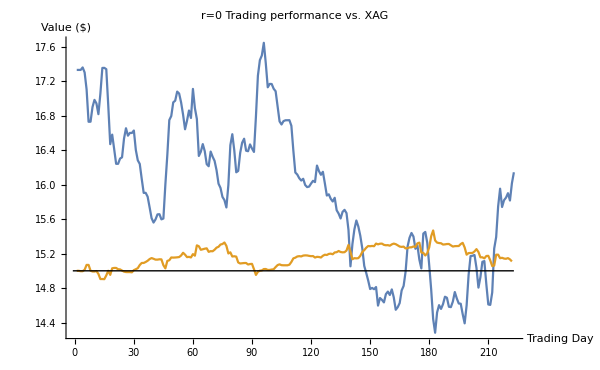

```mathematica
ListPlot[{pp@pricesSparse,valueSparse},Joined->True,ImageSize->600,AxesLabel->{"Trading Day", "Value ($)"},PlotLabel->"r=0 Trading performance vs. XAG",Epilog->Line[{{-1,invest},{Length@valueSparse+1,invest}}]]
```

```mathematica
FinancialData["SP500",{#,#}&@{2015,10,15}]
```

{{{2015,10,15},2023.86}}

```mathematica
FinancialData["SP500",{#,#}&@{2015,02,03}]
```

{{{2015,2,3},2050.03}}

```mathematica
(2050.030029-2023.859985)/2050.030029
```

0.0127657

```mathematica
stateSparse[[All,2]]*pricesSparse//Abs//Max//#/invest&
```

0.518701

```mathematica
invest=15;
rectifier=# UnitStep[#]&;
rs=Table[
r=i;
makeInvestmentSparse[{money_,ownedCommodities_},{edge_,currPrice_}]:=
With[{toSell=ownedCommodities*currPrice},With[{newMoney=money+toSell},
With[{toSpend=newMoney * Sign[edge]rectifier[Abs[edge]-r]/stddev^2},
With[{newCommodities=toSpend/currPrice,left=newMoney-toSpend},
{If[left<0, (*borrow*)left(1+r),left], newCommodities}]]]]
stateSparse=FoldList[makeInvestmentSparse,{invest, 0},{#["Returns"],#["Value"]}&/@joinedSparse];
pricesSparse=pp[#["Value"]&/@joinedSparse];
valueSparse=First/@stateSparse+stateSparse[[All,2]]*pricesSparse;
(Last@valueSparse-invest)/invest,{i,0,0.1,0.001}];
```

```mathematica
(valueSparse-invest)/invest//Last
```

0.00645196

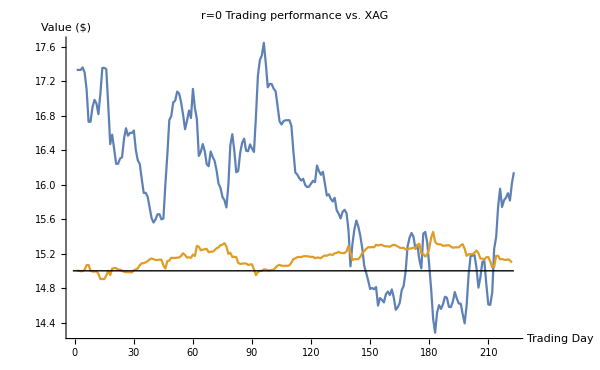

```mathematica
ListPlot[{pp@pricesSparse,valueSparse},Joined->True,ImageSize->600,AxesLabel->{"Trading Day", "Value ($)"},PlotLabel->"r=0 Trading performance vs. XAG",Epilog->Line[{{-1,invest},{Length@valueSparse+1,invest}}]]
```

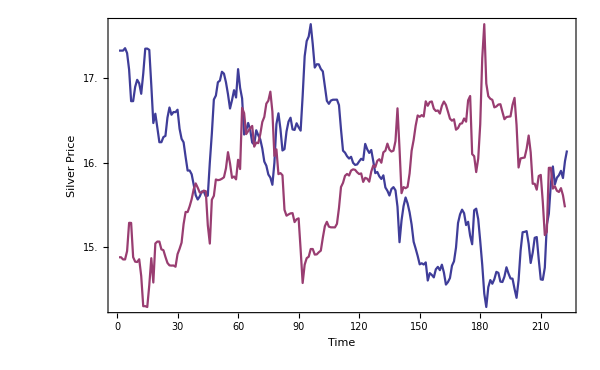
-Graphics-Ag PriceNet ValueTime

```mathematica
Labeled[Labeled[Labeled[TwoAxisListPlot[{pp@pricesSparse,valueSparse},{{Joined->True,ImageSize->600,AxesLabel->{"Time","Silver Price"}}, {Joined->True,ImageSize->600,AxesLabel->{"Time", "Net Value"}}}],"Ag Price", Left],"Net Value", Right],"Time", Bottom]
```

```mathematica
(* Two axis list plot adopted from docs *)
TwoAxisListPlot[{f_, g_}]:=TwoAxisListPlot[{f, g}, {{},{}}]
TwoAxisListPlot[{f_,g_},{{opts1___}, {opts2___}}, rTickAcc_Integer:4]:=Module[{fgraph,ggraph,frange,grange,fticks,gticks,fstyle, gstyle},
(*Extract plot style*)
fstyle = Sequence@@Cases[{opts1}, (PlotStyle->a_):>a];
gstyle = Sequence@@Cases[{opts2}, (PlotStyle->a_):>a];
fgraph=ListPlot[f,Axes->True,PlotStyle->{ColorData[1][1], fstyle}, opts1];
ggraph=ListPlot[g,Axes->True,PlotStyle->{ColorData[1][2], gstyle}, opts2];
{frange,grange}=(PlotRange/.AbsoluteOptions[#,PlotRange])[[2]]&/@{fgraph,ggraph};fticks=N@FindDivisions[frange,5];gticks=N@Quiet@Transpose@{fticks,ToString[NumberForm[#,rTickAcc],StandardForm]&/@Rescale[fticks,frange,grange]};Show[fgraph,ggraph/.Graphics[graph_,s___]:>Graphics[GeometricTransformation[graph,RescalingTransform[{{0,1},grange},{{0,1},frange}]],s],Axes->False,Frame->True,FrameStyle->{ColorData[1]/@{1,2},{Automatic,Automatic}},FrameTicks->{{fticks,gticks},{Automatic,Automatic}}]]
```